# Práctica 1

## Convolución de dos variables discretas

### Ejemplo: Convolución de dos variables Poisson X \[Distributed] P[2], Y \[Distributed] P[3]

```mathematica
(* Funciones de probabilidad*)

PDF[PoissonDistribution[2],x]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
PDF[PoissonDistribution[3],x]
```

Piecewise[{{3^x/(ⅇ^3 x!), x≥0}, {0, True}}]

```mathematica
(* Función de probabilidad de la convolución *)

fconvolucion[z_] := DiscreteConvolve[PDF[PoissonDistribution[2],x],PDF[PoissonDistribution[3],x],x,z]
fconvolucion[z]
```

Piecewise[{{5^z/(ⅇ^5 z!), z≥0}, {0, True}}]

```mathematica
(* Construcción del modelo a partir de la función de probabilidad*)

Convolucion1 = ProbabilityDistribution[fconvolucion[z],{z,0,Infinity,1}]
```

ProbabilityDistribution[Piecewise[{{5^x/(ⅇ^5 x!), x≥0}, {0, True}}],{x,0,∞,1}]

```mathematica
(* Construcción del modelo directamente *)

TransformedDistribution[X1 + X2, {X1 \[Distributed] PoissonDistribution[Subscript[λ, 1]], X2 \[Distributed] PoissonDistribution[Subscript[λ, 2]]}]
```

PoissonDistribution[λ_1+λ_2]

## Convolución de dos variables continuas

### Ejemplo: Convolución de una variable uniforme X \[Distributed] U[-1,1] con una triangular Y \[Distributed] T[-2,2]

Piecewise[{{1/2, -1≤x≤1}, {0, True}}]

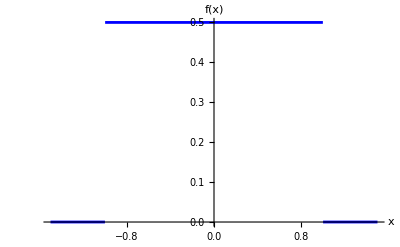

Piecewise[{{(2+y)/4, -2≤y≤0}, {(2-y)/4, 0<y≤2}, {0, True}}]

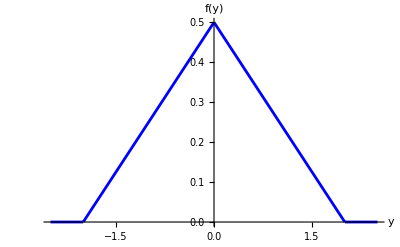

```mathematica
(*Funciones de densidad de una variable con distribución U[-1,1] y de una T[-2,2]*)

PDF[UniformDistribution[{-1,1}],x]
Plot[PDF[UniformDistribution[{-1,1}],x], {x, -1.5,1.5}, PlotRange->{{-1.5,1.5},Automatic}, AxesLabel->{x,f[x]},PlotStyle->Blue]
PDF[TriangularDistribution[{-2,2}],y]
Plot[PDF[TriangularDistribution[{-2,2}],y], {y, -2.5,2.5}, PlotRange->{{-2.5,2.5},Automatic}, AxesLabel->{y,f[y]},PlotStyle->Blue]
```

```mathematica
(* Función de densidad de la convolución *)

fconvolucion[z_]:=Convolve[PDF[UniformDistribution[{-1,1}],x],PDF[TriangularDistribution[{-2,2}],x],x,z]
fconvolucion[z]
```

Piecewise[{{1/8 (3-z^2), -1<z≤1}, {1/16 (-3+z)^2, 1<z<3}, {1/16 (3+z)^2, -3<z≤-1}, {0, True}}]

ProbabilityDistribution[Piecewise[{{1/8 (3-x^2), -1<x≤1}, {1/16 (-3+x)^2, 1<x<3}, {1/16 (3+x)^2, -3<x≤-1}, {0, True}}],{x,-∞,∞}]

Piecewise[{{1, x≥3}, {1/24 (12+9 x-x^3), -1<x≤1}, {1/48 (21+27 x-9 x^2+x^3), 1<x<3}, {1/48 (27+27 x+9 x^2+x^3), -3<x≤-1}, {0, True}}]

Piecewise[{{1, x≥3}, {1/24 (12+9 x-x^3), -1<x≤1}, {1/48 (21+27 x-9 x^2+x^3), 1<x<3}, {1/48 (27+27 x+9 x^2+x^3), -3<x≤-1}, {0, True}}]

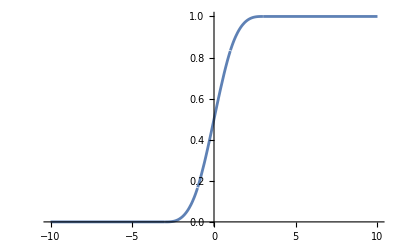

```mathematica
(* Construcci.08.08ón del modelo a partir de la función de densidad *)

Convolucion1 = ProbabilityDistribution[Convolve[PDF[UniformDistribution[{-1,1}],x],PDF[TriangularDistribution[{-2,2}],x],x,z],{z,-Infinity,Infinity}]
Z[x_] = CDF[Convolucion1,x]
Z [x]
Plot[Z[x],{x,-10,10}]
```

```mathematica
(* Función de distribución de la convolución*)

Convolve[PDF[UniformDistribution[{-1,1}],x],CDF[TriangularDistribution[{-2,2}],x],x,z]
Simplify[%]
```

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {1/48 (3+z)^3, -3<z≤-1}, {1/24 (12+9 z-z^3), -1<z<1}, {1/48 (17+21 z+3 z^2-z^3), z==1}, {1/48 (21+27 z-9 z^2+z^3), 1<z<3}, {0, True}}]

Piecewise[{{1, z≥3}, {1/48 (3+z)^3, -3<z≤-1}, {1/24 (12+9 z-z^3), -1<z≤1}, {1/48 (21+27 z-9 z^2+z^3), 1<z<3}, {0, True}}]

```mathematica
(*Función de distribución de la convolución*)

Probability[X1 + X2 <= z, {X1 \[Distributed] UniformDistribution[{-1,1}], X2 \[Distributed] TriangularDistribution[{-2,2}]}]
```

Piecewise[{{1, z>3}, {1/48 (3+z)^3, -3≤z≤-1}, {1/24 (12+9 z-z^3), -1<z≤1}, {1/48 (21+27 z-9 z^2+z^3), 1<z≤3}, {0, True}}]

```mathematica
(* Construcción del modelo a partir de la función de distribución *)

Convolucion1 = ProbabilityDistribution[{"CDF", Convolve[PDF[UniformDistribution[{-1,1}],x],PDF[TriangularDistribution[{-2,2}],x],x,z]}, {z,-Infinity, Infinity}]
CDF[Convolucion1,x]
Simplify[%]
```

ProbabilityDistribution[Piecewise[{{1/8 (-3+x), 1<x<3}, {-x/4, -1<x≤1}, {(3+x)/8, -3<x≤-1}, {0, True}}],{x,-∞,∞}]

Piecewise[{{1/8 (3-x^2), -1<x≤1}, {1/16 (9-6 x+x^2), 1<x<3}, {1/16 (9+6 x+x^2), -3<x≤-1}, {0, True}}]

Piecewise[{{1/8 (3-x^2), -1<x≤1}, {1/16 (-3+x)^2, 1<x<3}, {1/16 (3+x)^2, -3<x≤-1}, {0, True}}]

## Convolución de una continua con una mixta

### Ejemplo: Convolución de una variable mixta con una función de distribución dada y una variable con distribución uniforme Y \[Distributed] U[0,2]

MixtureDistribution[{3/4,1/4},{ProbabilityDistribution[Piecewise[{{1/3, -2≤x≤1}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1, x==1}, {0, True}}],{x,1,1,1}]}]

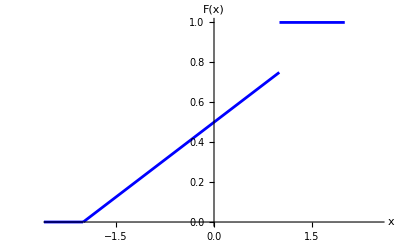

Piecewise[{{y/2, 0≤y≤2}, {1, y>2}, {0, True}}]

Piecewise[{{1/2, 0≤y≤2}, {0, True}}]

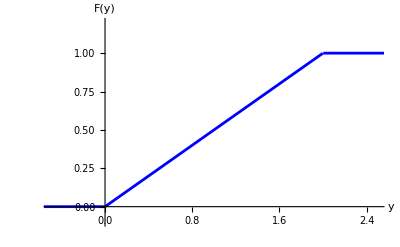

```mathematica
(* Construcción de un modelo mixto a partir de la función de distribución*)


(* La variable X es una mixtura de una distribución  uniforme en [-2,1] y una degenerada en 1, con pesos 3/4 y 1/4 *)
ModeloX = ProbabilityDistribution[{"CDF",Piecewise[{{0, x < -2}, {(x+2)/4, -2 <= x < 1}, {1, x >= 1}}]}, {x, -Infinity, Infinity}]
Plot[CDF[ModeloX,x],{x,-3,2},PlotRange->{{-2.5,2.5}, Automatic}, AxesLabel->{x, F[x]}, PlotStyle->Blue]

(* La variable Y es uniforme en [0,2] *)

CDF[UniformDistribution[{0,2}],y]
PDF[UniformDistribution[{0,2}],y]
Plot[CDF[UniformDistribution[{0,2}],y],{y,-3,3}, PlotRange->{{-0.5,2.5},{-0.1,1.2}}, AxesLabel->{y,F[y]}, PlotStyle->Blue]

(* Convolución de las funciones de distribución; integrando respecto de Y, que es absolutamente continua *)
```

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

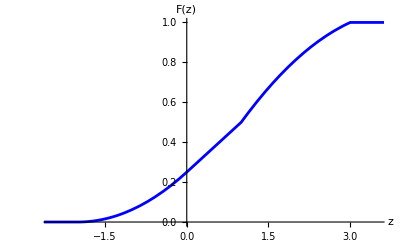

```mathematica
(* Función de distribución de la convolución *)

FConvolucion[z_]:= Convolve[PDF[UniformDistribution[{0,2}],x],CDF[ModeloX,x],x,z]
FConvolucion[z]
Plot[FConvolucion[z],{z,-3,4}, PlotRange->{{-2.5,3.5}, Automatic}, AxesLabel->{z,F[z]}, PlotStyle->Blue]
```

```mathematica
(* Función de distribución de la convolución mediante la definición *)

Integrate[CDF[ModeloX,z-x]PDF[UniformDistribution[{0,2}],x],{x,0,2}]
Simplify[%]

(* Obtención de la función de distribución calculando la distribución de la suma de variables *)

Probability[X+Y <= z, {X \[Distributed] ModeloX, Y \[Distributed] UniformDistribution[{0,2}]}]
Simplify[%]

(* Obtención de la función de densidad, a partir de la función de distribución *)
```

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (4+4 z+z^2), -2<z≤0}, {0, True}}]

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

Piecewise[{{1, z>3}, {1/2 (-1+z), z==3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (4+4 z+z^2), -2<z≤0}, {0, True}}]

Piecewise[{{1, z≥3}, {(1+z)/4, 0<z≤1}, {1/16 (1+8 z-z^2), 1<z<3}, {1/16 (2+z)^2, -2<z≤0}, {0, True}}]

Piecewise[{{0, z<-2||z==-2}, {(2+z)/8, -2<z<0}, {1/4, z==0||0<z<1}, {1/16 (8-2 z), 1<z<3}, {0, z>3}, {Indeterminate, True}}]

Piecewise[{{1/4, 0≤z<1}, {(4-z)/8, 1<z<3}, {(2+z)/8, -2<z<0}, {0, z≤-2||z>3}, {Indeterminate, True}}]

Piecewise[{{0, z<-2||z==-2}, {1/16 (4+2 z), -2<z<0}, {1/4, z==0||0<z<1}, {1/16 (8-2 z), 1<z<3}, {0, z>3}, {Indeterminate, True}}]

Piecewise[{{1/4, 0≤z<1}, {(4-z)/8, 1<z<3}, {(2+z)/8, -2<z<0}, {0, z≤-2||z>3}, {Indeterminate, True}}]

ProbabilityDistribution[Piecewise[{{1/4, 0<x≤1}, {1/16 (8-2 x), 1<x<3}, {(2+x)/8, -2<x≤0}, {0, True}}],{x,-∞,∞}]

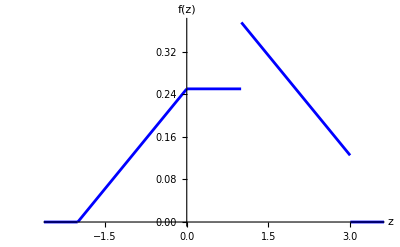

Piecewise[{{1, x==1}, {0, True}}]

1/4 (Piecewise[{{1/2, 1≤z≤3}, {0, True}}])+3/4 (Piecewise[{{1/3, 0<z≤1}, {(3-z)/6, 1<z<3}, {(2+z)/6, -2<z≤0}, {0, True}}])

```mathematica
(* Función de densidad, derivando la función de distribución *)

D[FConvolucion[z],z]
Simplify[%]
FConvolucion'[z]
Simplify[%]

(* Definiendo el modelo *)
ModeloConvolucion = ProbabilityDistribution[{"CDF", FConvolucion[z]},{z, -Infinity, Infinity}]
Plot[PDF[ModeloConvolucion,z],{z,-3,4},PlotRange->{{-2.5,3.5}, Automatic}, AxesLabel->{z,f[z]}, PlotStyle->Blue]

(* Podemos determinar la función de densidad, integrando respecto de X 

Determinamos la convolución de la parte continua y la parte discreta de X, y hacemos la mixtura *)

partediscretaX[x_]:=Piecewise[{{1, x==1}}]
partediscretaX[x]
3/4Convolve[PDF[UniformDistribution[{-2,1}],x],PDF[UniformDistribution[{0,2}],x],x,z] + 1/4DiscreteConvolve[partediscretaX[x], PDF[UniformDistribution[{0,2}],x],x,z]
Simplify[%]
```

## Convolución de dos distribuciones mixtas

### Funciones de distribución

MixtureDistribution[{2/3,1/3},{ProbabilityDistribution[Piecewise[{{1/2, -1≤x≤1}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1, x==1}, {0, True}}],{x,1,1,1}]}]

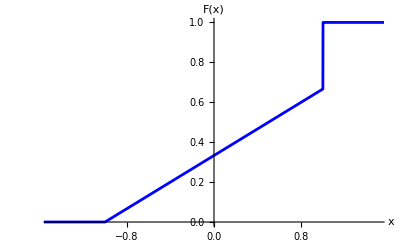

MixtureDistribution[{4/7,3/7},{ProbabilityDistribution[Piecewise[{{1/2, 0≤x<2}, {0, True}}],{x,-∞,∞}],ProbabilityDistribution[Piecewise[{{1/3, x==2}, {2/3, x==4}, {0, True}}],{x,2,4,1}]}]

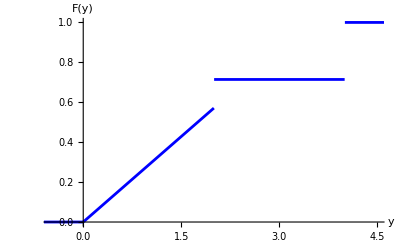

```mathematica
(* La variable X es una mixtura de una distribución uniforme en[-1,1]y una degenerada en 1, con pesos 2/3 y 1/3. *)

ModeloX = ProbabilityDistribution[{"CDF", Piecewise[{{0, x < -1}, {(x+1)/3, -1 <= x <= 1}, {1, x >=1}}]}, {x,-Infinity, Infinity}]

(* La variable Y es una mixtura con pesos 4/7 y 3/7 de una distribución uniforme en [0,2] y una discreta que toma valores 2 y 4 con probabilidades 1/3 y 2/3  *)

Plot[CDF[ModeloX,x], {x,-2,2}, PlotRange->{{-1.5,1.5},Automatic}, AxesLabel->{x,F[x]}, PlotStyle->Blue]

ModeloY = ProbabilityDistribution[{"CDF", Piecewise[{{0, x <0},{2x/7, 0 <= x <= 2}, {5/7, 2 <= x <= 4},{1, x>=4}}]}, {x,-Infinity, Infinity}]

Plot[CDF[ModeloY,x],{x,-1,5},PlotRange->{{-0.5,4.5}, Automatic}, AxesLabel->{y,F[y]}, PlotStyle->Blue]
```

### Convolución de las funciones de distribución, integrando respecto de X

```mathematica
(* Determinamos la convolución de la parte continua y la parte discreta de X, y hacemos la mixtura *)

2/3Convolve[PDF[UniformDistribution[{-1,1}],x], Piecewise[{{0, x <0},{2x/7, 0 <= x < 2}, {5/7, 2 <= x <4},{1, x >= 4}}],x,z] + 1/3DiscreteConvolve[Piecewise[{{1, x ==1}}],Piecewise[{{0, x <0},{2x/7, 0 <= x < 2}, {5/7, 2 <= x <4},{1, x >= 4}}],x,z]
Simplify[%]
```

1/3 (Piecewise[{{5/7, 3≤z<5}, {1, z≥5}, {2/7 (-1+z), 1≤z<3}, {0, True}}])+2/3 (Piecewise[{{1, z>5}, {-5/14 (-5+z), z==3}, {1/2 (-3+z), z==5}, {(2+z)/7, 3<z<5}, {1/14 (3+2 z-z^2), z==1}, {1/14 (-2+7 z-z^2), 1<z<3}, {1/14 (1+2 z+z^2), -1<z<1}, {0, True}}])

Piecewise[{{1, z≥5}, {1/21 (1+z)^2, -1<z<1}, {1/21 (9+2 z), 3≤z<5}, {1/21 (-4+9 z-z^2), 1≤z<3}, {0, True}}]

### Convolución de las funciones de distribución, integrando respecto de Y

```mathematica
(* Determinamos la convolución de la parte continua y la parte discreta de Y, y hacemos la mixtura *)

4/7Convolve[PDF[UniformDistribution[{0,2}],x], Piecewise[{{0, x <-1},{(x+1)/3, -1 <= x < 1}, {1, x >= 1}}],x,z] + DiscreteConvolve[Piecewise[{{1/7, x ==2},{2/7, x==4}}],Piecewise[{{0, x <-1},{(x+1)/3, -1 <= x < 1}, {1, x >= 1}}],x,z]
Simplify[%]
```

(Piecewise[{{3/7, z≥5}, {1/21 (-1+z), 1≤z<3}, {1/21 (-3+2 z), 3≤z<5}, {0, True}}])+4/7 (Piecewise[{{1, z≥3}, {1/12 (-3+8 z-z^2), 1≤z<3}, {1/12 (1+z)^2, -1<z<1}, {0, True}}])

Piecewise[{{1, z≥5}, {1/21 (1+z)^2, -1<z<1}, {1/21 (9+2 z), 3≤z<5}, {1/21 (-4+9 z-z^2), 1≤z<3}, {0, True}}]

## Convergencia en distribución

### Problema 4

```mathematica
(* Definición de la variable aleatoria mediante una función a trozos *)
Xn[n_,ω_] := Piecewise[{{n*(n*ω -1), 0 <= ω < 1/n},{0, 1/n <= ω < 2},{1, 2 <= ω < n},{n, ω>= n}}]
Xn[n,ω]

ProbabilidadOmega[λ_,ω_] := CDF[ExponentialDistribution[Xn[n,ω]],ω]
```

Piecewise[{{n (-1+n ω), 0≤ω<1/n}, {0, 1/n≤ω<2}, {1, 2≤ω<n}, {n, ω≥n}, {0, True}}]

```mathematica
(* Construcción del modelo Fn *)

Fn[x_, n_, λ_] := Probability[Xn[n,Omega] <= x, Omega \[Distributed] ExponentialDistribution[λ], Assumptions->n >= 3]
Fn[x,n,λ]
Simplify[%]
```

Piecewise[{{1, n-x≤0}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {ⅇ^(-n λ) (-1+ⅇ^(n λ)), x≥1&&n-x>0}, {ⅇ^(-((n+x) λ)/n^2) (-1+ⅇ^(((n+x) λ)/n^2)), n+x>0&&x<0}, {0, True}}]

Piecewise[{{1, n≤x}, {1-ⅇ^(-2 λ), 0≤x<1}, {1-ⅇ^(-n λ), x≥1&&n>x}, {1-ⅇ^(-((n+x) λ)/n^2), n+x>0&&x<0}, {0, True}}]

```mathematica
(* Límite de la sucesión de funciones de distribución y convergencia débil *)
DiscreteLimit[Fn[x,n,λ], n -> Infinity, Assumptions->λ>0]
```

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Piecewise[{{1, ω≥2}, {-∞, ω==0}, {0, True}}]

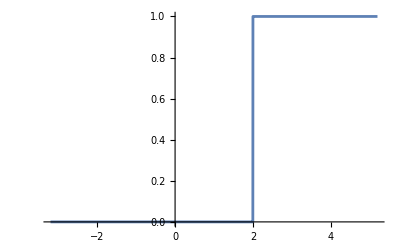

Piecewise[{{1, x≥1}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {0, True}}]

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Piecewise[{{1, n-x≤0}, {(-1+ⅇ^2)/ⅇ^2, 0≤x<1}, {ⅇ^-n (-1+ⅇ^n), x≥1&&n-x>0}, {ⅇ^(-1/n-x/n^2) (-1+ⅇ^(1/n+x/n^2)), n+x>0&&x<0}, {0, True}}]

Piecewise[{{1, x≥3}, {(-1+ⅇ^2)/ⅇ^2, 0≤x<1}, {(-1+ⅇ^3)/ⅇ^3, 1≤x<3}, {ⅇ^(-1/3-x/9) (-1+ⅇ^(1/3+x/9)), -3<x<0}, {0, True}}]

Piecewise[{{1, x≥3}, {1-1/ⅇ^2, 0≤x<1}, {1-1/ⅇ^3, 1≤x<3}, {1-ⅇ^(-1/3-x/9), -3<x<0}, {0, True}}]

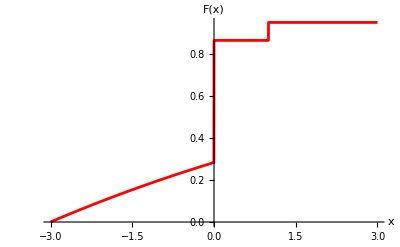

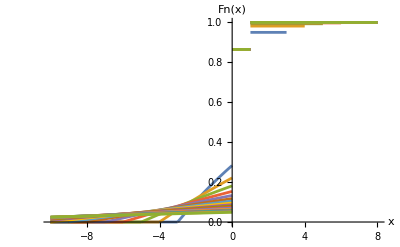

```mathematica
(* Límite de la sucesión de variables aleatorias y convergencia en distribución *)

Xlimit[ω_] := DiscreteLimit[Xn[n,ω], n-> Infinity]
Xlimit[ω]
Plot[Xlimit[ω],{ω,-3.2,5.2}]
CDF[TransformedDistribution[Xlimit[Omega], Omega \[Distributed] ExponentialDistribution[λ]],x]
Simplify[%]

(* Funciones de distribución*)

Fn[x,n,1]
Fn[x,3,1]
Simplify[%]
Plot[Fn[x,3,1], {x, -3, 3}, PlotStyle->Red, AxesLabel->{x,F[x]}]
Plot[Evaluate[Table[Fn[x,n,1],{n,3,20}],{x,-10,8}], AxesLabel->{x,Fn[x]}]
```